4.54133 (-0.243717+s) (3.55162/Df0[s]-2.55084/DSigma[s])

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

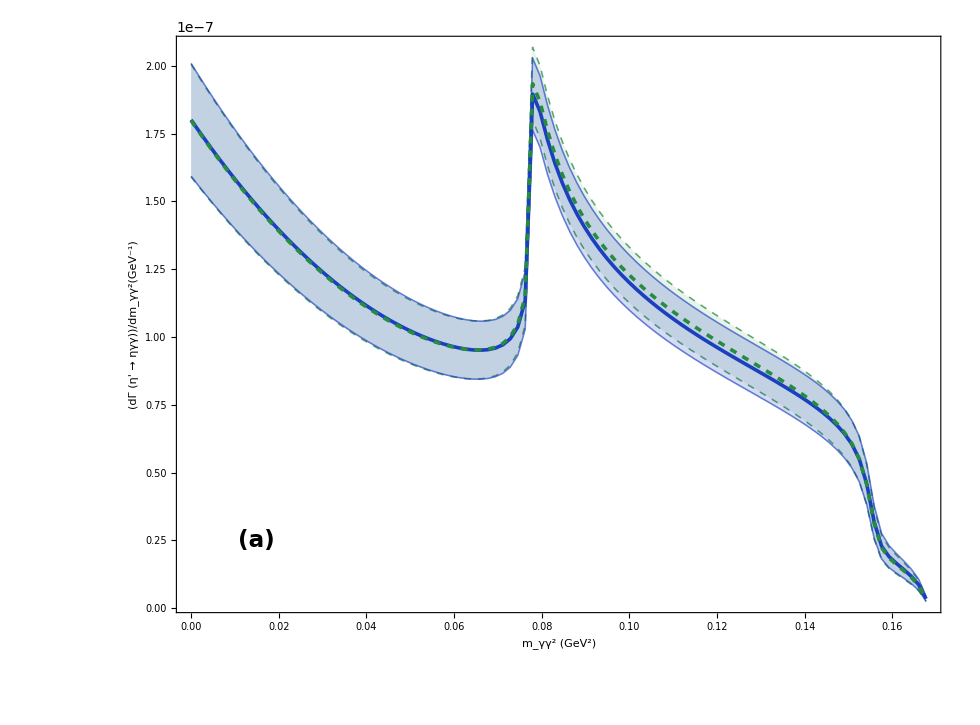

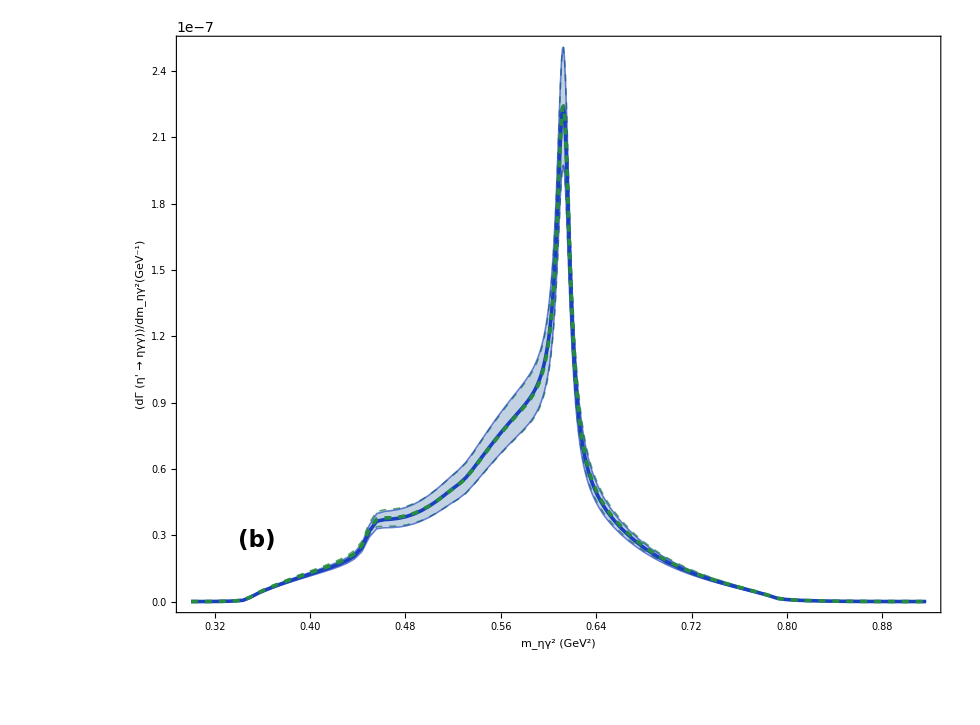

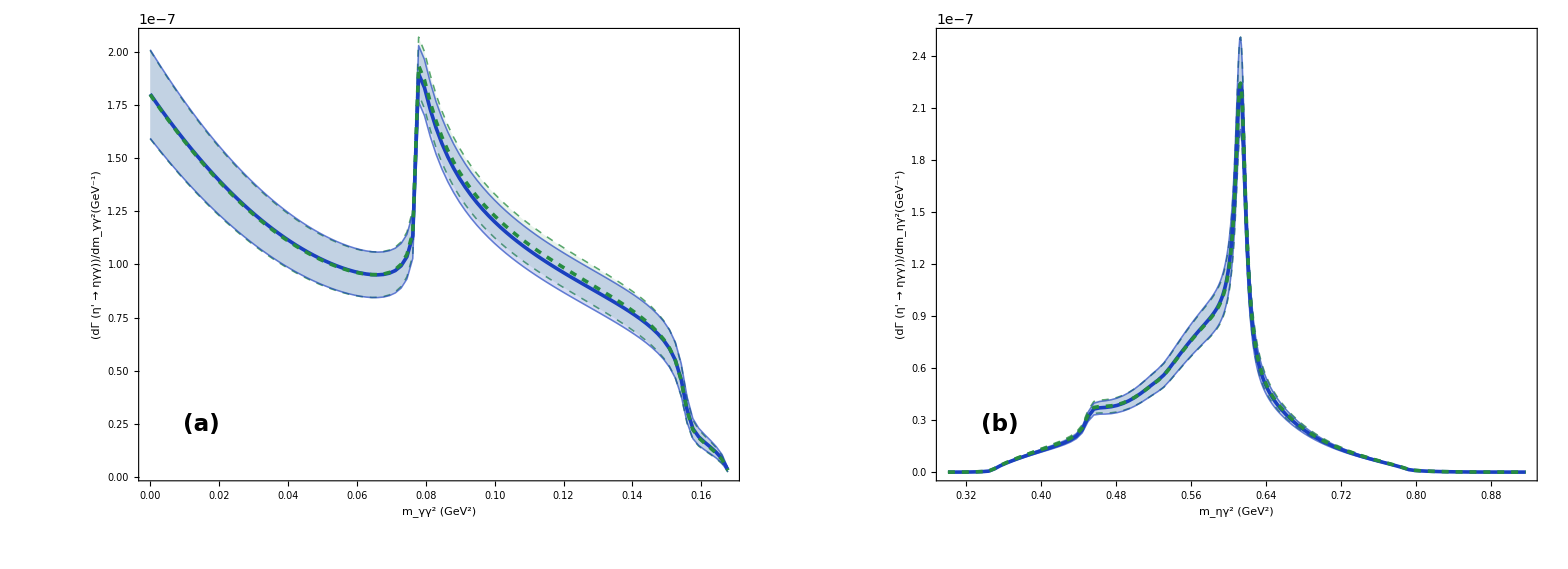

<|WidthSM→1.800.2010^-8,BranchingSM→0.0000960.000011,WidthSMPlusVB→1.780.2010^-8,BranchingSMPlusVB→0.0000950.000011,WidthPureContinuousVB2→1.40.410^-11,BranchingPureContinuousVB2→7.62.110^-8,PureContinuousVB2Fraction→0.000800.00021,WidthOnShellEffective→1.780.2010^-8,BranchingOnShellEffective→0.0000950.000011,OnShellEffectiveFraction→0.999200.00021,WidthNetVB→-1.450.2210^-10,BranchingNetVB→-7.71.210^-7,RelativeVBShift→-0.00810.0017,WidthVBInterference→-1.600.2510^-10,BranchingVBInterference→-8.51.310^-7,CouplingCoefficient→0.0000850.000011,Yukawa2Cs2Ms6MB2→0.0000850.000011|>

Dataset[<>]

<|WidthSM_eV→18.02.0,WidthSMPlusVB_eV→17.82.0,WidthPureContinuousVB2_eV→0.0140.004,WidthOnShellEffective_eV→17.82.0|>

<|VMDPhotonExchangeSymmetryResidual→0.,DarkPhotonExchangeSymmetryResidual→1.73472×10^-18,InterferencePhotonExchangeSymmetryResidual→0.,DarkToSMLimitVMDResidual→0.,DarkToSMLimitInterferenceResidual→0.,LSMNormalizationResidual→0.,MinimumSampledSMTotalMatrixElementSquared→4.13317×10^-6,MinimumSampledDarkTotalMatrixElementSquared→3.63182×10^-6,GammaGammaGridPointCount→100,EtaGammaGridPointCount→202,CentralGammaGammaCurveNumericQ→True,CentralEtaGammaCurveNumericQ→True|>

```mathematica
(* 0. Global settings *)
ClearAll["Global`*"];

(*
 The central curves are evaluated once at the central input values.
 nRuns controls only the Monte-Carlo uncertainty bands and integrated
 uncertainty propagation; it is not used to smooth the central curves.
*)
nRuns = 100;
nGridGG = 100;
nGridEtaGBase = 100;
nGridOmega = 101;
omegaGridHalfWidths = 6.;

safetySigma = 5;
eps = 10^-7;

(* One-dimensional adaptive integration settings.  The phase-space
   prefactor is kept outside NIntegrate so the integrator works on a
   well-scaled matrix-element integral. *)
accGoal1D = 10;
precGoal1D = 8;
minRec1D = 2;
maxRec1D = 40;

ProgressStatus[label_, i_, total_] :=
  Row[{label, ": ", ProgressIndicator[i, {0, total}], "  ", i, "/", total}];

CouplingCoeffCentralInput = 0.0000853727272727272;
CouplingCoeffUncertaintyInput = 0.000010835775045318799;

(* 1. Random inputs *)
GenerateValue[central_?NumericQ, sigma_?NumericQ] :=
  If[sigma == 0, central, RandomVariate[NormalDistribution[central, sigma]]];

SetRandomInputs[central_: False] :=
 Module[{draw},
  draw[value_?NumericQ, sigma_?NumericQ] :=
    If[TrueQ[central], value, GenerateValue[value, sigma]];

  (* New-physics coefficient *)
  BestCouplingCoeff =
    draw[CouplingCoeffCentralInput, CouplingCoeffUncertaintyInput];
  BestYukawa2Cs2Ms6MB2 = BestCouplingCoeff;

  (* Electromagnetic and decay constants *)
  alpha = draw[7.297525664*10^-3, 0.000000017*10^-3];
  fK = 110.10*10^-3;
  fPi = 92.07*10^-3;

  (* External masses and total width *)
  mEta = draw[547.862*10^-3, 0.017*10^-3];
  mEtaPrime = draw[957.78*10^-3, 0.06*10^-3];
  mPiCharged = draw[139.57039*10^-3, 0.00018*10^-3];
  mKCharged = draw[493.677*10^-3, 0.016*10^-3];
  gammaEtaPrimeTotal = draw[0.188*10^-3, 0.006*10^-3];

  (* Vector masses and widths *)
  mRho = draw[775.26*10^-3, 0.23*10^-3];
  mOmega = draw[782.66*10^-3, 0.13*10^-3];
  mPhi = draw[1019.461*10^-3, 0.016*10^-3];

  gammaRho = draw[149.1*10^-3, 0.8*10^-3];
  gammaOmega = draw[8.68*10^-3, 0.13*10^-3];
  gammaPhi = draw[4.249*10^-3, 0.013*10^-3];

  (* Nucleon and scalar-sector inputs *)
  mN = draw[938.27208816*10^-3, 0.00000029*10^-3];
  mSigma = 498*10^-3;
  mf0 = 990*10^-3;
  ma0 = 980*10^-3;
  phiS = -8 Degree;

  (* VMD phenomenological inputs *)
  gVMD = draw[0.70, 0.01];
  zSmBm = draw[0.65, 0.01];
  phiP = draw[41.4, 0.5] Degree;
  phiV = draw[3.3, 0.1] Degree;
  zNS = draw[0.83, 0.02];

  (* Eta and eta-prime radiative couplings *)
  gRhoEtaGamma = gVMD*zNS*Cos[phiP];
  gRhoEtaPrimeGamma = gVMD*zNS*Sin[phiP];

  gOmegaEtaGamma =
    gVMD/3*(zNS*Cos[phiP]*Cos[phiV] -
       2*zSmBm*Sin[phiP]*Sin[phiV]);

  gOmegaEtaPrimeGamma =
    gVMD/3*(zNS*Sin[phiP]*Cos[phiV] +
       2*zSmBm*Cos[phiP]*Sin[phiV]);

  gPhiEtaGamma =
    gVMD/3*(zNS*Cos[phiP]*Sin[phiV] +
       2*zSmBm*Sin[phiP]*Cos[phiV]);

  gPhiEtaPrimeGamma =
    gVMD/3*(zNS*Sin[phiP]*Sin[phiV] -
       2*zSmBm*Cos[phiP]*Cos[phiV]);

  cRho = gRhoEtaGamma*gRhoEtaPrimeGamma;
  cOmega = gOmegaEtaGamma*gOmegaEtaPrimeGamma;
  cPhi = gPhiEtaGamma*gPhiEtaPrimeGamma;

  (* Scalar self-energy couplings *)
  gSigmaPiPiSq =
    3*(mPiCharged^2 - mSigma^2)^2*Cos[phiS]^2/(2*fPi^2);

  gSigmaKKBarSq =
    (mKCharged^2 - mSigma^2)^2*
      (Cos[phiS] - Sqrt[2]*Sin[phiS])^2/(2*fK^2);

  gf0PiPiSq =
    3*(mPiCharged^2 - mf0^2)^2*Sin[phiS]^2/(2*fPi^2);

  gf0KKBarSq =
    (mKCharged^2 - mf0^2)^2*
      (Sin[phiS] + Sqrt[2]*Cos[phiS])^2/(2*fK^2);
 ];

SetRandomInputs[True];

(* 2. Kinematics and VMD *)
Kallen[x_?NumericQ, y_?NumericQ, z_?NumericQ] :=
  x^2 + y^2 + z^2 - 2*x*y - 2*x*z - 2*y*z;

sGG[t_?NumericQ, u_?NumericQ] := mEtaPrime^2 + mEta^2 - t - u;

uMin[t_?NumericQ] := mEta^2*mEtaPrime^2/t;
uMax[t_?NumericQ] := mEtaPrime^2 + mEta^2 - t;

tMinAtS[s_?NumericQ] :=
  (mEtaPrime^2 + mEta^2 - s -
     Sqrt[Max[0, Kallen[mEtaPrime^2, mEta^2, s]]])/2;

tMaxAtS[s_?NumericQ] :=
  (mEtaPrime^2 + mEta^2 - s +
     Sqrt[Max[0, Kallen[mEtaPrime^2, mEta^2, s]]])/2;

Constraint[t_?NumericQ, u_?NumericQ] :=
  Boole[
    mEta^2 <= t <= mEtaPrime^2 &&
    uMin[t] <= u <= uMax[t]
  ];

gammaRhoEff[t_?NumericQ] :=
  If[
   t > 4*mPiCharged^2,
   gammaRho*
    ((t - 4*mPiCharged^2)/(mRho^2 - 4*mPiCharged^2))^(3/2),
   0.
  ];

AtSM[t_?NumericQ] :=
  cRho/(mRho^2 - t - I*mRho*gammaRhoEff[t]) +
  cPhi/(mPhi^2 - t - I*mPhi*gammaPhi) +
  cOmega/(mOmega^2 - t - I*mOmega*gammaOmega);

AuSM[u_?NumericQ] := AtSM[u];

DarkContact[kappa_?NumericQ] :=
  kappa*(4*64*mN^6/alpha)*cOmega;

AtDark[t_?NumericQ, kappa_?NumericQ] := AtSM[t] + DarkContact[kappa];
AuDark[u_?NumericQ, kappa_?NumericQ] := AuSM[u] + DarkContact[kappa];

Btt[t_?NumericQ, u_?NumericQ] :=
  1/8*(t^2 + mEtaPrime^4)*sGG[t, u]^2 +
  1/8*(mEtaPrime^2 - t)*(mEtaPrime^2 - u)*
   (t*u + mEtaPrime^2*(t + u - mEtaPrime^2 - 2*mEta^2));

Buu[t_?NumericQ, u_?NumericQ] :=
  1/8*(u^2 + mEtaPrime^4)*sGG[t, u]^2 +
  1/8*(mEtaPrime^2 - t)*(mEtaPrime^2 - u)*
   (t*u + mEtaPrime^2*(t + u - mEtaPrime^2 - 2*mEta^2));

Btu[t_?NumericQ, u_?NumericQ] :=
  1/8*(t*u + mEtaPrime^4)*sGG[t, u]^2 +
  1/8*(mEtaPrime^2 - t)*(mEtaPrime^2 - u)*
   (t*u + mEtaPrime^2*(t + u - mEtaPrime^2 - 2*mEta^2));

VMDCore[t_?NumericQ, u_?NumericQ, at_?NumericQ, au_?NumericQ] :=
  Btt[t, u]*Abs[at]^2 +
  2*Btu[t, u]*Re[at*Conjugate[au]] +
  Buu[t, u]*Abs[au]^2;

MatrixVMD[t_?NumericQ, u_?NumericQ] :=
  VMDCore[t, u, AtSM[t], AuSM[u]]*Constraint[t, u];

MatrixVMDDark[t_?NumericQ, u_?NumericQ, kappa_?NumericQ] :=
  VMDCore[t, u, AtDark[t, kappa], AuDark[u, kappa]]*
   Constraint[t, u];

MatrixPureContact[t_?NumericQ, u_?NumericQ, kappa_?NumericQ] :=
 Module[{d = DarkContact[kappa]},
  VMDCore[t, u, d, d]*Constraint[t, u]
 ];

(* 3. Scalar sector and full matrix element *)
EqualMassLoopReal[s_?NumericQ, mass_?NumericQ] :=
 Which[
  s <= 0, 0.,
  s < 4*mass^2,
   Module[{b = Sqrt[4*mass^2/s - 1]},
    2 - 2*ArcTan[1/b]*b
   ],
  s > 4*mass^2,
   Module[{b = Sqrt[1 - 4*mass^2/s]},
    2 - Log[(1 + b)/(1 - b)]*b
   ],
  True, 2.
 ];

EqualMassLoopImagBeta[s_?NumericQ, mass_?NumericQ] :=
  If[s > 4*mass^2, Sqrt[1 - 4*mass^2/s], 0.];

RSigma[s_?NumericQ] :=
  gSigmaKKBarSq/(16*Pi^2)*EqualMassLoopReal[s, mKCharged] +
  gSigmaPiPiSq/(16*Pi^2)*EqualMassLoopReal[s, mPiCharged];

ISigma[s_?NumericQ] :=
  -gSigmaKKBarSq/(16*Pi)*EqualMassLoopImagBeta[s, mKCharged] -
  gSigmaPiPiSq/(16*Pi)*EqualMassLoopImagBeta[s, mPiCharged];

DSigma[s_?NumericQ] :=
  s - mSigma^2 + I*ISigma[s] - RSigma[mSigma^2] + RSigma[s];

Rf0[s_?NumericQ] :=
  gf0KKBarSq/(16*Pi^2)*EqualMassLoopReal[s, mKCharged] +
  gf0PiPiSq/(16*Pi^2)*EqualMassLoopReal[s, mPiCharged];

If0[s_?NumericQ] :=
  -gf0KKBarSq/(16*Pi)*EqualMassLoopImagBeta[s, mKCharged] -
  gf0PiPiSq/(16*Pi)*EqualMassLoopImagBeta[s, mPiCharged];

Df0[s_?NumericQ] :=
  s - mf0^2 + I*If0[s] - Rf0[mf0^2] + Rf0[s];

gSigmaEtaEtaPrime :=
  Sin[2*phiP]/(2*fPi)*
   (
    (-ma0^2 + mEta^2*Cos[phiP]^2 +
       mEtaPrime^2*Sin[phiP]^2)*
      (Cos[phiS] + Sqrt[2]*(-1 + 2*fK/fPi)*Sin[phiS])
    -
    (-mEta^2 + mEtaPrime^2)*
      (Cos[2*phiP]*Cos[phiS] -
       1/2*Sin[2*phiP]*Sin[phiS])
   );

gf0EtaEtaPrime :=
  Sin[2*phiP]/(2*fPi)*
   (
    (-ma0^2 + mEta^2*Cos[phiP]^2 +
       mEtaPrime^2*Sin[phiP]^2)*
      (Sin[phiS] - Sqrt[2]*(-1 + 2*fK/fPi)*Cos[phiS])
    -
    (-mEta^2 + mEtaPrime^2)*
      (Cos[2*phiP]*Sin[phiS] +
       1/2*Sin[2*phiP]*Cos[phiS])
   );

AKKToEtaEtaPrime[s_?NumericQ] :=
  -((1 - 2*(-1 + 2*fK/fPi))*(s - mKCharged^2)*
      Sin[2*phiP])/(4*fK*fPi)
  +
  (s - mKCharged^2)/(2*fK)*
   (
    gf0EtaEtaPrime*(Sqrt[2]*Cos[phiS] + Sin[phiS])/Df0[s]
    +
    gSigmaEtaEtaPrime*(Cos[phiS] - Sqrt[2]*Sin[phiS])/DSigma[s]
   )
  -
  1/(4*fPi^2)*
   (
    (-8*mKCharged^2/9 - (mEta^2 + mEtaPrime^2)/3 -
       2*mPiCharged^2/9 + s)*
      (Sqrt[2]*Cos[2*phiP] + 1/2*Sin[2*phiP])
    +
    4/9*(2*mKCharged^2 - mPiCharged^2)*
      (-Cos[2*phiP]/Sqrt[2] + 2*Sin[2*phiP])
   );

APiPiToEtaEtaPrime[s_?NumericQ] :=
  (s - mPiCharged^2)/fPi*
   (
    gf0EtaEtaPrime*Sin[phiS]/Df0[s] +
    gSigmaEtaEtaPrime*Cos[phiS]/DSigma[s]
   )
  +
  (2*mPiCharged^2 - s)*Sin[2*phiP]/(2*fPi^2);

LoopF[z_?NumericQ] :=
 Which[
  z < 1/4,
   1/4*(-I*Pi + Log[(1 + Sqrt[1 - 4*z])/
       (1 - Sqrt[1 - 4*z])])^2,
  z > 1/4,
   -ArcSin[1/(2*Sqrt[z])]^2,
  True,
   -Pi^2/4
 ];

LoopL[z_?NumericQ] :=
  If[
   Abs[z] < 10^-4,
   1/24 + z/180 + z^2/1120 + z^3/6300,
   -1/(2*z) - 2*LoopF[1/z]/z^2
  ];

ScalarLoopFactor[s_?NumericQ] :=
  If[
   s <= 0,
   0.,
   LoopL[s/mKCharged^2]*AKKToEtaEtaPrime[s]/mKCharged^2 +
   LoopL[s/mPiCharged^2]*APiPiToEtaEtaPrime[s]/mPiCharged^2
  ];

LSM[t_?NumericQ, u_?NumericQ] :=
 Module[{s = sGG[t, u]},
  If[
   s <= 0,
   0.,
   2*alpha^2/Pi^2*s^2*Abs[ScalarLoopFactor[s]]^2*
    Constraint[t, u]
  ]
 ];

InterferenceWithAmplitudes[
   t_?NumericQ, u_?NumericQ, at_?NumericQ, au_?NumericQ] :=
 Module[{s = sGG[t, u]},
  If[
   s <= 0,
   0.,
   Re[
     -(alpha/Pi)*ScalarLoopFactor[s]*
      Conjugate[t*at + u*au]*s^2
    ]*Constraint[t, u]
  ]
 ];

Interference[t_?NumericQ, u_?NumericQ] :=
  InterferenceWithAmplitudes[t, u, AtSM[t], AuSM[u]];

InterferenceDark[t_?NumericQ, u_?NumericQ, kappa_?NumericQ] :=
  InterferenceWithAmplitudes[
   t, u, AtDark[t, kappa], AuDark[u, kappa]];

MatrixSMTotal[t_?NumericQ, u_?NumericQ] :=
  MatrixVMD[t, u] + Interference[t, u] + LSM[t, u];

MatrixDarkTotal[t_?NumericQ, u_?NumericQ, kappa_?NumericQ] :=
  MatrixVMDDark[t, u, kappa] +
  InterferenceDark[t, u, kappa] +
  LSM[t, u];

PhaseSpacePrefactor[] := 1/(2*256*mEtaPrime^3*Pi^3);

(* 4. Differential spectra: stable resonance-aware integration *)

VectorPoleSquares[] := {mRho^2, mOmega^2, mPhi^2};

InteriorIntegrationPoints[lo_?NumericQ, hi_?NumericQ, points_List] :=
 Module[{selected},
  selected = Select[N[points], lo < # < hi &];
  DeleteDuplicates[Sort[selected], Abs[#1 - #2] < 10^-12 &]
 ];

SetAttributes[NInt1D, HoldAll];

NInt1D[integrand_, var_Symbol, lo_, hi_, points_ : {}] :=
 Module[{loN, hiN, pointValues, iterator},
  loN = N[lo];
  hiN = N[hi];

  If[! NumericQ[loN] || ! NumericQ[hiN] || hiN <= loN,
   Return[0.]
  ];

  pointValues = InteriorIntegrationPoints[loN, hiN, N[points]];
  iterator = Join[{var, loN}, pointValues, {hiN}];

  NIntegrate[
   integrand,
   Evaluate[iterator],
   AccuracyGoal -> accGoal1D,
   PrecisionGoal -> precGoal1D,
   MinRecursion -> minRec1D,
   MaxRecursion -> maxRec1D,
   Method -> {
    "GlobalAdaptive",
    "SymbolicProcessing" -> 0
   }
  ]
 ];

GammaGammaBreakpoints[s_?NumericQ] :=
 Module[{sumTU = mEtaPrime^2 + mEta^2 - s, poles},
  poles = VectorPoleSquares[];
  Join[poles, sumTU - poles]
 ];

GammaGammaIntegralSM[s_?NumericQ] :=
 If[
  0 < s < (mEtaPrime - mEta)^2,
  NInt1D[
   MatrixSMTotal[t, mEtaPrime^2 + mEta^2 - s - t],
   t,
   tMinAtS[s],
   tMaxAtS[s],
   GammaGammaBreakpoints[s]
  ],
  0.
 ];

GammaGammaIntegralDark[s_?NumericQ, kappa_?NumericQ] :=
 If[
  0 < s < (mEtaPrime - mEta)^2,
  NInt1D[
   MatrixDarkTotal[t, mEtaPrime^2 + mEta^2 - s - t, kappa],
   t,
   tMinAtS[s],
   tMaxAtS[s],
   GammaGammaBreakpoints[s]
  ],
  0.
 ];

GammaGammaIntegralPureContact[s_?NumericQ, kappa_?NumericQ] :=
 If[
  0 < s < (mEtaPrime - mEta)^2,
  NInt1D[
   MatrixPureContact[t, mEtaPrime^2 + mEta^2 - s - t, kappa],
   t,
   tMinAtS[s],
   tMaxAtS[s],
   GammaGammaBreakpoints[s]
  ],
  0.
 ];

EtaGammaIntegralSM[t_?NumericQ] :=
 If[
  mEta^2 < t < mEtaPrime^2,
  NInt1D[
   MatrixSMTotal[t, u],
   u,
   uMin[t],
   uMax[t],
   VectorPoleSquares[]
  ],
  0.
 ];

EtaGammaIntegralDark[t_?NumericQ, kappa_?NumericQ] :=
 If[
  mEta^2 < t < mEtaPrime^2,
  NInt1D[
   MatrixDarkTotal[t, u, kappa],
   u,
   uMin[t],
   uMax[t],
   VectorPoleSquares[]
  ],
  0.
 ];

EtaGammaIntegralPureContact[t_?NumericQ, kappa_?NumericQ] :=
 If[
  mEta^2 < t < mEtaPrime^2,
  NInt1D[
   MatrixPureContact[t, u, kappa],
   u,
   uMin[t],
   uMax[t],
   VectorPoleSquares[]
  ],
  0.
 ];

GammaGammaSpectrum[s_?NumericQ] :=
  PhaseSpacePrefactor[]*GammaGammaIntegralSM[s];

GammaGammaSpectrumDark[s_?NumericQ, kappa_?NumericQ] :=
  PhaseSpacePrefactor[]*GammaGammaIntegralDark[s, kappa];

GammaGammaSpectrumPureContact[s_?NumericQ, kappa_?NumericQ] :=
  PhaseSpacePrefactor[]*GammaGammaIntegralPureContact[s, kappa];

EtaGammaSpectrum[t_?NumericQ] :=
  PhaseSpacePrefactor[]*EtaGammaIntegralSM[t];

EtaGammaSpectrumDark[t_?NumericQ, kappa_?NumericQ] :=
  PhaseSpacePrefactor[]*EtaGammaIntegralDark[t, kappa];

EtaGammaSpectrumPureContact[t_?NumericQ, kappa_?NumericQ] :=
  PhaseSpacePrefactor[]*EtaGammaIntegralPureContact[t, kappa];

GammaGammaSpectrumOnShellEffective[s_?NumericQ, kappa_?NumericQ] :=
  GammaGammaSpectrumDark[s, kappa] -
  GammaGammaSpectrumPureContact[s, kappa];

EtaGammaSpectrumOnShellEffective[t_?NumericQ, kappa_?NumericQ] :=
  EtaGammaSpectrumDark[t, kappa] -
  EtaGammaSpectrumPureContact[t, kappa];

(* 5. Common grids, central spectra, and spectrum Monte Carlo *)
mEtaNom = 547.862*10^-3;
dmEtaNom = 0.017*10^-3;
mEtaPrimeNom = 957.78*10^-3;
dmEtaPrimeNom = 0.06*10^-3;

mRhoNom = 775.26*10^-3;
gammaRhoNom = 149.1*10^-3;
mOmegaNom = 782.66*10^-3;
gammaOmegaNom = 8.68*10^-3;

xGGmin = eps;
xGGmax =
  (mEtaPrimeNom - safetySigma*dmEtaPrimeNom -
    (mEtaNom + safetySigma*dmEtaNom))^2 - eps;

xEtaGmin = (mEtaNom + safetySigma*dmEtaNom)^2 + eps;
xEtaGmax = (mEtaPrimeNom - safetySigma*dmEtaPrimeNom)^2 - eps;

xGridGG = N@Subdivide[xGGmin, xGGmax, nGridGG - 1];

omegaTWidthNom = mOmegaNom*gammaOmegaNom;
omegaGridMin =
  Max[xEtaGmin, mOmegaNom^2 - omegaGridHalfWidths*omegaTWidthNom];
omegaGridMax =
  Min[xEtaGmax, mOmegaNom^2 + omegaGridHalfWidths*omegaTWidthNom];

xGridEtaG =
 DeleteDuplicates[
  Sort@N@Join[
    Subdivide[xEtaGmin, xEtaGmax, nGridEtaGBase - 1],
    Subdivide[omegaGridMin, omegaGridMax, nGridOmega - 1],
    {mRhoNom^2, mOmegaNom^2}
   ],
  Abs[#1 - #2] < 10^-12 &
 ];

RunSpectrumAtCurrentInputs[] :=
 <|
  "ggDark" ->
   Table[{x, GammaGammaSpectrumDark[x, BestCouplingCoeff]},
    {x, xGridGG}],

  "ggSM" ->
   Table[{x, GammaGammaSpectrum[x]}, {x, xGridGG}],

  "etaGDark" ->
   Table[{x, EtaGammaSpectrumDark[x, BestCouplingCoeff]},
    {x, xGridEtaG}],

  "etaGSM" ->
   Table[{x, EtaGammaSpectrum[x]}, {x, xGridEtaG}]
 |>;

RunCentralSpectrum[] :=
 Module[{},
  SetRandomInputs[True];
  RunSpectrumAtCurrentInputs[]
 ];

RunOneSpectrum[seed_Integer] :=
 BlockRandom[
  SeedRandom[seed];
  SetRandomInputs[False];
  RunSpectrumAtCurrentInputs[]
 ];

centralSpectra =
 Monitor[
  RunCentralSpectrum[],
  ProgressStatus["Central theory spectra", 1, 1]
 ];

spectrumRunCounter = 0;

spectrumRuns =
 Monitor[
  Table[
   spectrumRunCounter = i;
   RunOneSpectrum[10000 + i],
   {i, nRuns}
  ],
  ProgressStatus[
   "EtaPrime -> Eta gamma gamma spectrum Monte Carlo",
   spectrumRunCounter,
   nRuns
  ]
 ];

CurveStats[runs_, key_, centralCurve_] :=
 Module[{xs, central, matrix, columns, mean, sigma},
  xs = centralCurve[[All, 1]];
  central = centralCurve[[All, 2]];
  matrix = (#[key][[All, 2]] & /@ runs);
  columns = Transpose[matrix];
  mean = Mean /@ columns;
  sigma =
   If[
    Length[runs] < 2,
    ConstantArray[0, Length[xs]],
    StandardDeviation /@ columns
   ];

  <|
   "Central" -> centralCurve,
   "Mean" -> Transpose[{xs, mean}],
   "Sigma" -> Transpose[{xs, sigma}],
   "Upper" -> Transpose[{xs, central + sigma}],
   "Lower" -> Transpose[{xs, central - sigma}]
  |>
 ];

ggDarkStats =
  CurveStats[spectrumRuns, "ggDark", centralSpectra["ggDark"]];
ggSMStats =
  CurveStats[spectrumRuns, "ggSM", centralSpectra["ggSM"]];

etaGDarkStats =
  CurveStats[spectrumRuns, "etaGDark", centralSpectra["etaGDark"]];
etaGSMStats =
  CurveStats[spectrumRuns, "etaGSM", centralSpectra["etaGSM"]];

(* 6. Theory-only spectrum figures *)
colNP = RGBColor[0.10, 0.25, 0.75];
colSM = RGBColor[0.15, 0.55, 0.25];

bandStyleDark = Directive[colNP, Opacity[0.18]];
bandStyleSM = Directive[colSM, Opacity[0.10]];

bandEdgeDark =
  Directive[colNP, Opacity[0.65], AbsoluteThickness[1.15]];

bandEdgeSM =
  Directive[colSM, Opacity[0.75], Dashed, AbsoluteThickness[1.15]];

MakeBand[stat_, fillStyle_, edgeStyle_] :=
 Show[
  ListLinePlot[
   {stat["Upper"], stat["Lower"]},
   InterpolationOrder -> 1,
   PlotStyle -> {Directive[Opacity[0]], Directive[Opacity[0]]},
   Filling -> {1 -> {2}},
   FillingStyle -> fillStyle,
   Axes -> False,
   Frame -> False,
   PlotRange -> All
  ],
  ListLinePlot[
   {stat["Upper"], stat["Lower"]},
   InterpolationOrder -> 1,
   PlotStyle -> {edgeStyle, edgeStyle},
   Axes -> False,
   Frame -> False,
   PlotRange -> All
  ]
 ];

legendLines =
 LineLegend[
  {
   Directive[colNP, AbsoluteThickness[2.6]],
   Directive[colSM, Dashed, AbsoluteThickness[2.6]]
  },
  {"SM + \!\(\*SubscriptBox[\(V\), \(ℬ\)]\)", "SM only"},
  LabelStyle -> Directive[Black, 18],
  LegendMarkerSize -> 25
 ];

bandLegend =
 SwatchLegend[
  {bandStyleDark, bandStyleSM},
  {"SM + \!\(\*SubscriptBox[\(V\), \(ℬ\)]\) \
±1σ", "SM only ±1σ"},
  LabelStyle -> Directive[Black, 18],
  LegendMarkerSize -> 27
 ];

legendBox =
 Framed[
  Column[{legendLines, bandLegend}, Spacings -> 0.18],
  FrameStyle -> Black,
  Background -> White,
  FrameMargins -> 5
 ];

commonFrameStyle = Directive[Black, AbsoluteThickness[1.25]];
commonLabelStyle = Directive[Black, 22];
commonTickStyle = Directive[Black, 20];
commonPlotRangePadding =
  {{Scaled[0.025], Scaled[0.035]},
   {Scaled[0.045], Scaled[0.075]}};
commonAspectRatio = 0.74;

GammaGammaPlot =
 Show[
  MakeBand[ggSMStats, bandStyleSM, bandEdgeSM],
  MakeBand[ggDarkStats, bandStyleDark, bandEdgeDark],
  ListLinePlot[
   {ggDarkStats["Central"], ggSMStats["Central"]},
   InterpolationOrder -> 1,
   PlotStyle ->
    {
     Directive[colNP, AbsoluteThickness[2.6]],
     Directive[colSM, Dashed, AbsoluteThickness[2.6]]
    }
  ],
  PlotRange -> All,
  Frame -> True,
  Axes -> False,
  FrameStyle -> commonFrameStyle,
  Background -> White,
  LabelStyle -> commonLabelStyle,
  TicksStyle -> commonTickStyle,
  FrameLabel ->
   {
    "\!\(\*SubsuperscriptBox[\(m\), \(γγ\), \(2\)]\) (\
\!\(\*SuperscriptBox[\(GeV\), \(2\)]\))",
   "\!\(\*FractionBox[\(dΓ \((η' → \\ \
ηγγ)\)\), SubsuperscriptBox[\(dm\), \(γγ\), \
\(2\)]]\)(\!\(\*SuperscriptBox[\(GeV\), \(-1\)]\))"
   },
  ImagePadding -> {{280, 45}, {115, 50}},
  ImageMargins -> {{60, 30}, {45, 45}},
  PlotRangePadding -> commonPlotRangePadding,
  PlotRangeClipping -> False,
  AspectRatio -> commonAspectRatio,
  ImageSize -> 980,
  Epilog ->
   {
    Inset[Style["(a)", 23, Bold, Black], Scaled[{0.105, 0.125}]],
    Inset[legendBox, Scaled[{0.975, 0.975}], {Right, Top}]
   }
 ];

EtaGammaPlot =
 Show[
  MakeBand[etaGSMStats, bandStyleSM, bandEdgeSM],
  MakeBand[etaGDarkStats, bandStyleDark, bandEdgeDark],
  ListLinePlot[
   {etaGDarkStats["Central"], etaGSMStats["Central"]},
   InterpolationOrder -> 1,
   PlotStyle ->
    {
     Directive[colNP, AbsoluteThickness[2.6]],
     Directive[colSM, Dashed, AbsoluteThickness[2.6]]
    }
  ],
  PlotRange -> All,
  Frame -> True,
  Axes -> False,
  FrameStyle -> commonFrameStyle,
  Background -> White,
  LabelStyle -> commonLabelStyle,
  TicksStyle -> commonTickStyle,
  FrameLabel ->
   {
    "\!\(\*SubsuperscriptBox[\(m\), \(ηγ\), \(2\)]\) (\!\
\(\*SuperscriptBox[\(GeV\), \(2\)]\))",
    "\!\(\*FractionBox[\(dΓ \((η' → \\ \
ηγγ)\)\), SubsuperscriptBox[\(dm\), \(ηγ\), \
\(2\)]]\)(\!\(\*SuperscriptBox[\(GeV\), \(-1\)]\))"
   },
  ImagePadding -> {{280, 45}, {115, 50}},
  ImageMargins -> {{60, 30}, {45, 45}},
  PlotRangePadding -> commonPlotRangePadding,
  PlotRangeClipping -> False,
  AspectRatio -> commonAspectRatio,
  ImageSize -> 980,
  Epilog ->
   {
    Inset[Style["(b)", 23, Bold, Black], Scaled[{0.105, 0.125}]],
    Inset[legendBox, Scaled[{0.975, 0.975}], {Right, Top}]
   }
 ];

TheorySpectraFigure =
 GraphicsRow[
  {GammaGammaPlot, EtaGammaPlot},
  Spacings -> 35,
  ImageSize -> 2180
 ];

GammaGammaPlot
EtaGammaPlot
TheorySpectraFigure

Export["etaPrime_eta_gamma_gamma_spectrum.pdf", GammaGammaPlot];
Export["etaPrime_eta_gamma_spectrum.pdf", EtaGammaPlot];
Export["etaPrime_eta_gamma_gamma_theory_spectra.pdf", TheorySpectraFigure];

(* 7. Total widths and uncertainty propagation *)
ClearAll[TotalWidthsAndBranchings, TotalSigma];

TotalWidthsAndBranchings[central_: False, seed_Integer : 0] :=
 BlockRandom[
  If[! TrueQ[central], SeedRandom[seed]];
  SetRandomInputs[central];

  Module[
   {
    integralSM,
    integralDark,
    integralPureContact,
    integralOnShellEffective,
    integralNetVB,
    integralVBInterference,
    widthSM,
    widthDark,
    widthPureContact,
    widthOnShellEffective,
    widthNetVB,
    widthVBInterference,
    branchingSM,
    branchingDark,
    branchingPureContact,
    branchingOnShellEffective,
    branchingNetVB,
    branchingVBInterference
   },

   (* Nested one-dimensional integrations are split explicitly at the
      vector-resonance positions in both invariant variables. *)
   integralSM =
    NInt1D[
     EtaGammaIntegralSM[t],
     t,
     mEta^2,
     mEtaPrime^2,
     VectorPoleSquares[]
    ];

   integralDark =
    NInt1D[
     EtaGammaIntegralDark[t, BestCouplingCoeff],
     t,
     mEta^2,
     mEtaPrime^2,
     VectorPoleSquares[]
    ];

   integralPureContact =
    NInt1D[
     EtaGammaIntegralPureContact[t, BestCouplingCoeff],
     t,
     mEta^2,
     mEtaPrime^2,
     VectorPoleSquares[]
    ];

   (* Same decomposition convention as the eta-prime -> pi0 gamma gamma notebook. *)
   integralOnShellEffective = integralDark - integralPureContact;
   integralNetVB = integralDark - integralSM;
   integralVBInterference = integralDark - integralSM - integralPureContact;

   widthSM = PhaseSpacePrefactor[]*integralSM;
   widthDark = PhaseSpacePrefactor[]*integralDark;
   widthPureContact = PhaseSpacePrefactor[]*integralPureContact;
   widthOnShellEffective = PhaseSpacePrefactor[]*integralOnShellEffective;
   widthNetVB = PhaseSpacePrefactor[]*integralNetVB;
   widthVBInterference = PhaseSpacePrefactor[]*integralVBInterference;

   branchingSM = widthSM/gammaEtaPrimeTotal;
   branchingDark = widthDark/gammaEtaPrimeTotal;
   branchingPureContact = widthPureContact/gammaEtaPrimeTotal;
   branchingOnShellEffective =
     widthOnShellEffective/gammaEtaPrimeTotal;
   branchingNetVB = widthNetVB/gammaEtaPrimeTotal;
   branchingVBInterference =
     widthVBInterference/gammaEtaPrimeTotal;

   <|
    "WidthSM" -> widthSM,
    "BranchingSM" -> branchingSM,

    "WidthSMPlusVB" -> widthDark,
    "BranchingSMPlusVB" -> branchingDark,

    "WidthPureContinuousVB2" -> widthPureContact,
    "BranchingPureContinuousVB2" -> branchingPureContact,
    "PureContinuousVB2Fraction" -> integralPureContact/integralDark,

    "WidthOnShellEffective" -> widthOnShellEffective,
    "BranchingOnShellEffective" -> branchingOnShellEffective,
    "OnShellEffectiveFraction" ->
      integralOnShellEffective/integralDark,

    "WidthNetVB" -> widthNetVB,
    "BranchingNetVB" -> branchingNetVB,
    "RelativeVBShift" -> integralNetVB/integralSM,

    "WidthVBInterference" -> widthVBInterference,
    "BranchingVBInterference" -> branchingVBInterference
   |>
  ]
 ];

centralTotals =
 Monitor[
  TotalWidthsAndBranchings[True],
  ProgressStatus["Central total widths", 1, 1]
 ];

totalRunCounter = 0;

totalRuns =
 Monitor[
  Table[
   totalRunCounter = i;
   TotalWidthsAndBranchings[False, 20000 + i],
   {i, nRuns}
  ],
  ProgressStatus[
   "Total-width Monte Carlo",
   totalRunCounter,
   nRuns
  ]
 ];

TotalSigma[key_] :=
 If[
  Length[totalRuns] < 2,
  0,
  StandardDeviation[#[key] & /@ totalRuns]
 ];

WidthCentral = centralTotals["WidthSM"];
BranchingTheoryCentral = centralTotals["BranchingSM"];
WidthDarkCentral = centralTotals["WidthSMPlusVB"];
BranchingDarkCentral = centralTotals["BranchingSMPlusVB"];

WidthPureContinuousVB2Central =
  centralTotals["WidthPureContinuousVB2"];
BranchingPureContinuousVB2Central =
  centralTotals["BranchingPureContinuousVB2"];
PureContinuousVB2FractionCentral =
  centralTotals["PureContinuousVB2Fraction"];

WidthOnShellEffectiveCentral =
  centralTotals["WidthOnShellEffective"];
BranchingOnShellEffectiveCentral =
  centralTotals["BranchingOnShellEffective"];
OnShellEffectiveFractionCentral =
  centralTotals["OnShellEffectiveFraction"];

WidthUncertainty = TotalSigma["WidthSM"];
BranchingTheoryUncertainty = TotalSigma["BranchingSM"];
WidthDarkUncertainty = TotalSigma["WidthSMPlusVB"];
BranchingDarkUncertainty = TotalSigma["BranchingSMPlusVB"];

WidthPureContinuousVB2Uncertainty =
  TotalSigma["WidthPureContinuousVB2"];
BranchingPureContinuousVB2Uncertainty =
  TotalSigma["BranchingPureContinuousVB2"];
PureContinuousVB2FractionUncertainty =
  TotalSigma["PureContinuousVB2Fraction"];

WidthOnShellEffectiveUncertainty =
  TotalSigma["WidthOnShellEffective"];
BranchingOnShellEffectiveUncertainty =
  TotalSigma["BranchingOnShellEffective"];
OnShellEffectiveFractionUncertainty =
  TotalSigma["OnShellEffectiveFraction"];

Yukawa2Cs2Ms6MB2Central = CouplingCoeffCentralInput;
Yukawa2Cs2Ms6MB2Uncertainty = CouplingCoeffUncertaintyInput;

resultKeys =
 {
  "WidthSM",
  "BranchingSM",
  "WidthSMPlusVB",
  "BranchingSMPlusVB",
  "WidthPureContinuousVB2",
  "BranchingPureContinuousVB2",
  "PureContinuousVB2Fraction",
  "WidthOnShellEffective",
  "BranchingOnShellEffective",
  "OnShellEffectiveFraction",
  "WidthNetVB",
  "BranchingNetVB",
  "RelativeVBShift",
  "WidthVBInterference",
  "BranchingVBInterference"
 };

FinalResults =
 Association[
  Table[
   key -> Around[centralTotals[key], TotalSigma[key]],
   {key, resultKeys}
  ]
 ];

FinalResults =
 Append[
  FinalResults,
  "CouplingCoefficient" ->
   Around[
    CouplingCoeffCentralInput,
    CouplingCoeffUncertaintyInput
   ]
 ];

FinalResults =
 Append[
  FinalResults,
  "Yukawa2Cs2Ms6MB2" ->
   Around[
    CouplingCoeffCentralInput,
    CouplingCoeffUncertaintyInput
   ]
 ];

ResultsDataset =
 Dataset[
  KeyValueMap[
   <|"Quantity" -> #1, "Result" -> #2|> &,
   FinalResults
  ]
 ];

FinalResults
ResultsDataset

WidthResultsEV =
 <|
  "WidthSM_eV" ->
   Around[
    10^9*centralTotals["WidthSM"],
    10^9*TotalSigma["WidthSM"]
   ],
  "WidthSMPlusVB_eV" ->
   Around[
    10^9*centralTotals["WidthSMPlusVB"],
    10^9*TotalSigma["WidthSMPlusVB"]
   ],
  "WidthPureContinuousVB2_eV" ->
   Around[
    10^9*centralTotals["WidthPureContinuousVB2"],
    10^9*TotalSigma["WidthPureContinuousVB2"]
   ],
  "WidthOnShellEffective_eV" ->
   Around[
    10^9*centralTotals["WidthOnShellEffective"],
    10^9*TotalSigma["WidthOnShellEffective"]
   ]
 |>;

WidthResultsEV

(* 8. Automated sanity checks *)
SetRandomInputs[True];

tTest = (mEta^2 + mEtaPrime^2)/2;
uTest = (uMin[tTest] + uMax[tTest])/2;

symmetrySM =
  Abs[MatrixVMD[tTest, uTest] - MatrixVMD[uTest, tTest]];

symmetryDark =
  Abs[
   MatrixVMDDark[tTest, uTest, CouplingCoeffCentralInput] -
   MatrixVMDDark[uTest, tTest, CouplingCoeffCentralInput]
  ];

symmetryInterference =
  Abs[Interference[tTest, uTest] - Interference[uTest, tTest]];

smLimitVMD =
  Abs[MatrixVMDDark[tTest, uTest, 0] - MatrixVMD[tTest, uTest]];

smLimitInterference =
  Abs[
   InterferenceDark[tTest, uTest, 0] -
   Interference[tTest, uTest]
  ];

scalarNormalizationCheck =
 Module[
  {
   s = sGG[tTest, uTest],
   lhs,
   rhs
  },
  lhs = LSM[tTest, uTest];
  rhs =
   2*alpha^2/Pi^2*s^2*
    Abs[ScalarLoopFactor[s]]^2*
    Constraint[tTest, uTest];
  Abs[lhs - rhs]
 ];

samplePoints =
 Flatten[
  Table[
   With[
    {
     t = tt,
     uLow = uMin[tt],
     uHigh = uMax[tt]
    },
    Table[{t, uLow + y*(uHigh - uLow)}, {y, 0.05, 0.95, 0.1}]
   ],
   {tt, mEta^2 + 0.05*(mEtaPrime^2 - mEta^2),
    mEtaPrime^2 - 0.05*(mEtaPrime^2 - mEta^2),
    0.1*(mEtaPrime^2 - mEta^2)}
  ],
  1
 ];

minimumSMMatrix =
  Min[MatrixSMTotal @@ # & /@ samplePoints];

minimumDarkMatrix =
  Min[
   MatrixDarkTotal[#[[1]], #[[2]], CouplingCoeffCentralInput] & /@
    samplePoints
  ];

SanityChecks =
 <|
  "VMDPhotonExchangeSymmetryResidual" -> symmetrySM,
  "DarkPhotonExchangeSymmetryResidual" -> symmetryDark,
  "InterferencePhotonExchangeSymmetryResidual" ->
    symmetryInterference,
  "DarkToSMLimitVMDResidual" -> smLimitVMD,
  "DarkToSMLimitInterferenceResidual" -> smLimitInterference,
  "LSMNormalizationResidual" -> scalarNormalizationCheck,
  "MinimumSampledSMTotalMatrixElementSquared" -> minimumSMMatrix,
  "MinimumSampledDarkTotalMatrixElementSquared" -> minimumDarkMatrix,
  "GammaGammaGridPointCount" -> Length[xGridGG],
  "EtaGammaGridPointCount" -> Length[xGridEtaG],
  "CentralGammaGammaCurveNumericQ" ->
    And @@ (NumericQ /@ centralSpectra["ggDark"][[All, 2]]),
  "CentralEtaGammaCurveNumericQ" ->
    And @@ (NumericQ /@ centralSpectra["etaGDark"][[All, 2]])
 |>;

SanityChecks
```

```mathematica
WidthCentral
```

1.79921×10^-8

```mathematica
WidthUncertainty
```

1.9982×10^-9

```mathematica
EngineeringForm[BranchingTheoryCentral]
```

95.7025×10^-6

```mathematica
EngineeringForm[BranchingTheoryUncertainty]
```

11.3861×10^-6

```mathematica
WidthDarkCentral
```

1.78469×10^-8

```mathematica
WidthDarkUncertainty
```

2.00533×10^-9

```mathematica
EngineeringForm[BranchingDarkCentral]
```

94.9301×10^-6

```mathematica
EngineeringForm[BranchingDarkUncertainty]
```

11.4168×10^-6

```mathematica
OnShellEffectiveFractionCentral
```

0.999196

```mathematica
OnShellEffectiveFractionUncertainty
```

0.000206972